# Data Science and Machine Learning

## Lab session 06: Classification

## The go-to function: Classify

Classify generates a ClassifierFunction, i.e. a function that classifies data into classes.

As with Predict, Classify can be used on many types of data, including numerical, textual, sounds, and images, as well as combinations of these.

Structure:
	Classify[{example_1→class_1,example_2→class_2,…}]
    	Classify[{example_1,example_2,…}→{class_1,class_2,…}]
          	Classify[<|class_1→{example_11,example_12,…},class_2→{example_21,…},…|>]
  
Each example can be a single data element, a list of data elements, an association of data elements, or a Dataset object. 

You can specify the Method used as an option. Methods include: LogisticRegression, DecisionTree, NearestNeighbors, RandomForest, etc.
	Classify[{example_1→class_1,example_2→class_2,…}, Method → "MethodName"]

### Built-in Classifiers

There exists many Built-in Classifiers, i.e. pre-trained classifiers, to classify texts and images:

```mathematica
Classify["Language","What is this"]
```

English

```mathematica
Classify["Sentiment", "Machine Learning is great!"]
Classify["Sentiment", "Programming is difficult"]
```

Positive

Negative

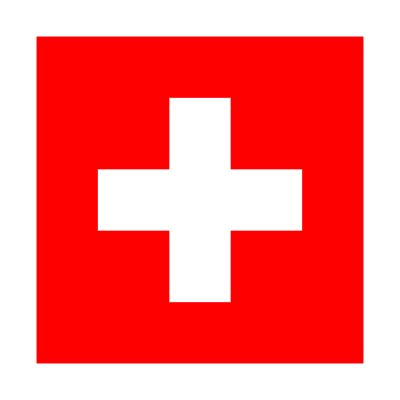
```mathematica
Classify["CountryFlag",-Graphics- ]
```

Switzerland

```mathematica
Classify["FacebookTopic", "The football game was delayed because of the snow", "TopProbabilities" -> 3]
```

{Weather→0.489744,Sports→0.40963,Leisure→0.0329668}

### Train your own Classifiers

```mathematica
trainingset = {{0.7,1.3} -> "A", {1.4,3.4} -> "A", {2.5,0.7} -> "A", {2.1,4.4} -> "B", {3.3,4.2} -> "B", {3.1,1.2} -> "B"};
ListPlot[trainingset]
```

-Graphics-

#### Train your Classifier

```mathematica
c =Classify[trainingset]
```

ClassifierFunction[…]

#### Get some information about your classifier

```mathematica
Information[c]
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,AB
Accuracy | (75.24.) %
Method | LogisticRegression
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 88.4 examples/ms
Loss | 0.52 ± 0.17
Model memory | 175. kB
Training examples used | 6 examples
Training time | 656. ms

```mathematica
Information[c,"Properties"]
```

{AcceptanceThreshold,Accuracy,AnomalyDetector,BatchEvaluationSpeed,BatchEvaluationTime,Calibrated,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,Function,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,MissingSynthesizer,OptimizationMethod,PerformanceGoal,ProbabilitiesFunction,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

#### Identify the class of an unlabeled example

```mathematica
c[{2.7,3.5}]
```

B

Instead of the class, you can obtain the Probabilities that your example belongs to one class or the other:

```mathematica
c[{2.7,3.5}, "Probabilities"]
```

<|A→1.80364×10^-10,B→1.|>

Plot the probability that the class of an example is "A", as function of the features:

```mathematica
Show[ContourPlot[c[{x,y}, "Probability" -> "A"], {x, 0, 5},{y,0,5}, PlotLegends -> Automatic], 
          ListPlot[trainingset, PlotStyle -> Black] ]
```

-Graphics-

#### Assess the accuracy of your classifier

```mathematica
testset = {{1.5,3} -> "A", {2.1,3.2} -> "A", {1.1,3.7} -> "A", {3.1,3.5} -> "B", {1.4,6.2} -> "B", {4.5,2.3} -> "B"};
```

ClassifierMeasurements yields a measurement report of your classifier, evaluated on a testing set:

```mathematica
cm =ClassifierMeasurements[c,testset]
```

Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 6
Accuracy | (83.17.) %
Accuracy baseline | (50.22.) %
Geometric mean of probabilities | 0.607 ± 0.32
Mean cross entropy | 0.5 ± 0.5
Single evaluation time | 3.29 ms/example
Batch evaluation speed | 813. examples/s
-Graphics- |

You can also directly obtain some properties:

```mathematica
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

0.833333

-Graphics-

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

## Applications

### Text Classification

We will use text from Wikipedia to train a topic classifier.

```mathematica
topics = {"Biology","Physics","Mathematics", "Economics"};
```

Extract data from Wikipedia:

```mathematica
texts=WikipediaData/@topics;
```

Train your classifier:

```mathematica
topicclassifier = Classify[texts ->topics]
```

ClassifierFunction[…]

Try to predict the topics...

```mathematica
topicclassifier["Statistics", "Probabilities"]
```

<|Biology→0.0033224,Economics→0.179691,Mathematics→0.805328,Physics→0.0116586|>

```mathematica
topicclassifier["The main cause of climate change is the emission of greenhouse gases. The combustion of fossil fuels for energy use creates most of these emissions. Agriculture, steel making, cement production, and forest loss are also significant sources.", "Probabilities"]
```

<|Biology→0.999026,Economics→0.000816757,Mathematics→0.0000948797,Physics→0.0000618898|>

### Image Classification

We will classify images based on their semantic features.

Define classes:

```mathematica
classes={"jellyfish","blackberry","octopus","blueberry"};
```

Extract images from the web using WebImageSearch

```mathematica
images=WebImageSearch[#,"Thumbnails",MaxItems->30] & /@classes;
```

```mathematica
images[[1,1]]
```

-Graphics-

Create your dataset:
We use Thread to create an association between our images and classes. Since we have a list of lists of images, we do a map with Thread so that to each image corresponds a class, and we then Flatten our list.

```mathematica
dataset=Flatten[Thread/@Thread[images->classes]];
```

```mathematica
nobs = Length[dataset]
```

120

We split our dataset into training and testing sets:

```mathematica
{trainingset,testset}=TakeDrop[RandomSample[dataset],Floor[nobs*0.6]];
```

We train our classifier:

```mathematica
cImage = Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
Information[cImage]
```

Classifier information
Data type | Image
Classes | ,,blackberryblueberryjellyfishoctopus
Accuracy | (96.71.5) %
Method | LogisticRegression
Single evaluation time | 126. ms/example
Batch evaluation speed | 8.33 examples/s
Loss | 0.228 ± 0.12
Model memory | 5.96 MB
Training examples used | 72 examples
Training time | 12.6 s
 |

Test the classifier:

```mathematica
test =RandomChoice[testset]
```

-Graphics-→jellyfish

```mathematica
cImage[First @test]
```

jellyfish

Assess the performance of your classifier:

```mathematica
cmImage = ClassifierMeasurements[cImage,testset]
```

Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 48
Accuracy | (97.92.1) %
Accuracy baseline | (40.7.) %
Geometric mean of probabilities | 0.674 ± 0.27
Mean cross entropy | 0.394 ± 0.39
Single evaluation time | 129. ms/example
Batch evaluation speed | 7.87 examples/s
-Graphics- |

Import the misclassified examples:

```mathematica
misClass = cmImage["WorstClassifiedExamples"->1]
```

{-Graphics-→jellyfish}

```mathematica
cImage[misClass[[1,1]]]
```

octopus

## Useful links

Introduction to WL: Machine Learning

Machine Learning functions

Classify